Exercises for Section 23 | More about Numbers

Find √2 to 500-digit precision. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
N[Sqrt[2],500]
```

1.4142135623730950488016887242096980785696718753769480731766797379907324784621070388503875343276415727350138462309122970249248360558507372126441214970999358314132226659275055927557999505011527820605714701095599716059702745345968620147285174186408891986095523292304843087143214508397626036279952514079896872533965463318088296406206152583523950547457502877599617298355752203375318570113543746034084988471603868999706990048150305440277903164542478230684929369186215805784631115966687130130156185689872372

Generate 10 random real numbers between 0 and 1. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
RandomReal[{0,1},10]
```

{0.619661,0.879452,0.482485,0.882765,0.802739,0.245494,0.476157,0.45883,0.460643,0.567642}

Make a plot of 200 points with random real x and y coordinates between 0 and 1. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListPlot[Table[{RandomReal[{0,1}],RandomReal[{0,1}]},200]]
```

-Graphics-

Create a random walk using AnglePath and 1000 random real numbers between 0 and 2π. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

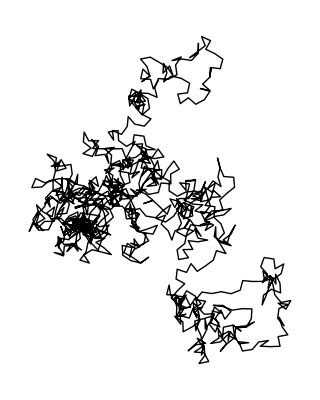

```mathematica
Graphics[Line[AnglePath[Table[RandomReal[{0,2Pi}],1000]]]]
```

Make a table of Mod[n^2,10] for n from 0 to 30. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Mod[n^2,10],{n,0,30}]
```

{0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0,1,4,9,6,5,6,9,4,1,0}

Make a line plot of Mod[n^n,10] for n from 1 to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Mod[n^n,10],{n,1,100}]]
```

-Graphics-

Make a table of the first 10 powers of π, rounded to integers. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Round[Pi^n],{n,10}]
```

{3,10,31,97,306,961,3020,9489,29809,93648}

Make a graph by connecting n with Mod[n^2,100] for n from 0 to 99. |

EXPECTED OUTPUT »

-Graphics- | ×

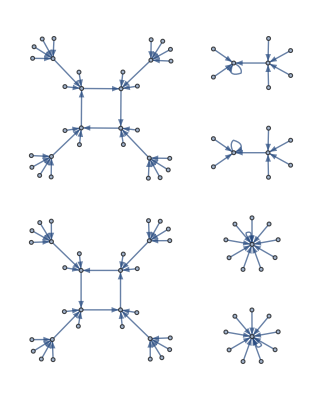

```mathematica
Graph[Table[n->Mod[n^2,100],{n,0,99}]]
```

Generate graphics of 50 circles with random real coordinates 0 to 10, random real radii from 0 to 2, and random colors. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

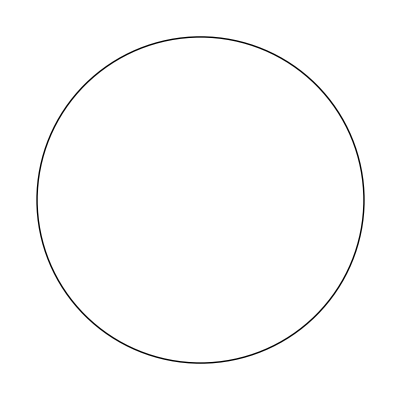

```mathematica
Graphics[Style[Circle[RandomReal[{0,10},2],RandomReal[{0,2}]],RandomColor[]]]
```

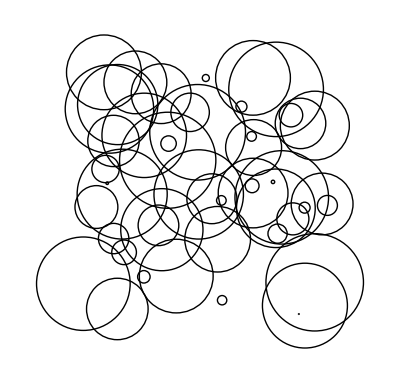

```mathematica
Graphics[Table[Style[Circle[{RandomReal[{0,10}],RandomReal[{0,10}]},RandomReal[{0,2}]],RandomColor[]],50]]
```

Make a plot of the nth prime divided by n*log(n), for n from 2 to 1000. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListPlot[Table[Prime[n]/(n*Log[n]),{n,2,1000}]]
```

-Graphics-

Make a line plot of the differences between successive primes up to 100. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[Table[Prime[n+1]-Prime[n],{n,100}]]
```

-Graphics-

Generate a sequence of 20 middle C notes with random durations between 0 and 0.5 seconds. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

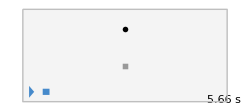

```mathematica
Sound[Table[SoundNote["C",RandomReal[{0,0.5}]],20]]
```

Make an array plot of Mod[i,j] for i and j up to 50. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ArrayPlot[Table[Mod[i,j],{i,50},{j,50}]]
```

-Graphics-

Make a list for n from 2 to 10 of array plots for x and y up to 50 of x^y mod n. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[ArrayPlot[Table[Mod[x^y,n],{x,50},{y,50}]],{n,2,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Use Round to compute the fractional part of π to 50 digits. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Round[N[Pi,50],5]
```

5

```mathematica
N[Pi-3,50]
```

0.14159265358979323846264338327950288419716939937511

```mathematica
Pi - Round[Pi]
```

-3+π

```mathematica
Round[Pi]
```

3

Find the sum of the first 1000 prime numbers. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Total[Table[Prime[n],{n,1000}]]
```

3682913

Make a list of the first 100 primes modulo 4. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[Mod[Prime[n],4],{n,100}]
```

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

Make a list of the first 10000 primes modulo 4, multiply them by 90° and create an angle path from them. |

EXPECTED OUTPUT »

-Graphics- | ×

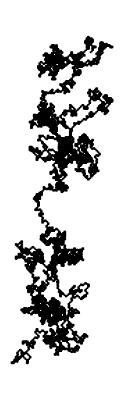

```mathematica
Graphics[Line[AnglePath[Table[Mod[Prime[n],4],{n,10000}]*90Degree]]]
```